#### Economics Equilibrium

```mathematica
dFun[p_,a_,b_]:=a-b*p
sFun[p_,c_,d_]:=c+d*p
pFun[α_,a_,b_,c_,d_]:=NDSolve[{D[p[x],x]-α*(dFun[p[x],a,b]-sFun[p[x],c,d])==0,p[0]==2},p,{x,0,20}]
```

```mathematica
Framed[Manipulate[Column[{ListLinePlot[{sFun[#[[1]],c,d]&/@Table[Evaluate[p[x]/.pFun[α,a,b,c,d]],{x,0,20}],dFun[#[[1]],a,b]&/@Table[Evaluate[p[x]/.pFun[α,a,b,c,d]],{x,0,20}]},AxesLabel->{"p"},PlotLegends->{"S(p)","D(p)"}],Plot[Evaluate[p[x]/.pFun[α,a,b,c,d]],{x,0,20},PlotRange->All,PlotStyle->Red,AxesLabel->{"t"},PlotLegends->{"P(t)"}]}],{{α,0.5},0,1},{{a,0.2},0.1,2},{{b,1},0.1,2},{{c,0.3},0.1,2},{{d,0.5},0.1,2},ControlPlacement->Left,Paneled->False],RoundingRadius->5]
```

```mathematica
init=5;
```

```mathematica
dFunNN[p_]:=1/p
sFunNN[p_]:=√p
pFunNN[α_]:=NDSolve[{D[p[x],x]-α(dFunNN[p[x]]-sFunNN[p[x]])==0,p[0]==init},p,{x,0,20}]
```

```mathematica
Framed[Manipulate[Plot[Evaluate[p[x]/.pFunNN[α]],{x,0,20},PlotRange->{Automatic,{0,init+1}},PlotStyle->Red,AxesLabel->{"t"},PlotLegends->{"P(t)"}],{{α,0.5},0,1},ControlPlacement->Left,Paneled->False],RoundingRadius->5]
```

```mathematica
pList=ConstantArray[0,20];
```

```mathematica
α=0.7;
a=0.3;
b=2;
c=0.2;
d=0.6;
```

```mathematica
sol2=Table[pList[[i+1]]=pList[[i]]+α(dFun[pList[[i]],a,b]-sFun[pList[[i]],c,d]),{i,20-1}]
```

{0.07,0.0126,0.059668,0.0210722,0.0527208,0.026769,0.0480494,0.0305995,0.0449084,0.0331751,0.0427964,0.0349069,0.0413763,0.0360714,0.0404214,0.0368544,0.0397794,0.0373809,0.0393477}

```mathematica
Framed[Manipulate[sol2=Table[pList[[i+1]]=pList[[i]]+α(dFun[pList[[i]],a,b]-sFun[pList[[i]],c,d]),{i,20-1}];Column[{ListLinePlot[sol2,AxesLabel->{"t"},PlotLegends->{"P(t)"}],ListLinePlot[{Transpose[{sol2,sFun[#,c,d]&/@sol2}],Transpose[{sol2,dFun[#,a,b]&/@sol2}]},AxesLabel->{"p"},PlotLegends->{"S(p)","D(p)"},PlotRange->{Automatic,Automatic}]}],{{α,0.7},0,1},{{a,0.3},0.1,2},{{b,2},0.1,2},{{c,0.2},0.1,2},{{d,0.6},0.1,2},ControlPlacement->Left,Paneled->False],RoundingRadius->5]
```

#### Valras Equilibrium

```mathematica
valrasFun[qeq_,peq_,b_,r_,qc_,a_]:=NDSolve[{D[q[t],t]+b(q[t]-qeq)+r(p[t]-peq)==0,D[p[t],t]+a(p[t]-peq)-qc(q[t]-qeq)==0,q[0]==5,p[0]==2},{q,p},{t,0,50}]
```

```mathematica
Framed[Manipulate[Plot[Evaluate[p[x]/.pFun[α,a,b,c,d]],{x,0,20},PlotRange->All,PlotStyle->Red],{{α,0.5},0,1},{{a,0.2},0.1,2},{{b,1},0.1,2},{{c,0.3},0.1,2},{{d,0.5},0.1,2},ControlPlacement->Left,Paneled->False],RoundingRadius->5]
```

```mathematica
sol1=valrasFun[2,3,1,1,1,0.4]
```

{{q→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

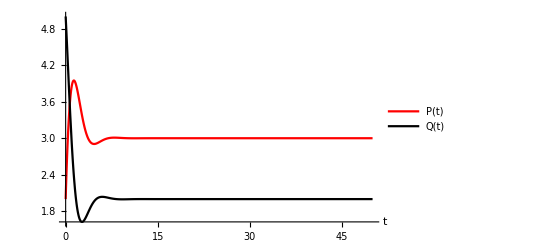

```mathematica
Plot[Evaluate[{p[x],q[x]}/.sol1[[1]]],{x,0,50},PlotStyle->{Red,Black},AxesLabel->{"t"},PlotLegends->{"P(t)","Q(t)"}]
```

```mathematica
qeq=1;
peq=2;
```

```mathematica
Framed[Manipulate[Plot[Evaluate[{p[x],q[x]}/.valrasFun[qeq,peq,b,r,qc,a][[1]]],{x,0,50},PlotRange->All,PlotStyle->{Red,Black},AxesLabel->{"t"},PlotLegends->{"P(t)","Q(t)"}],{{a,0.5},0,1},{{b,1},0.1,2},{{r,0.3},0.1,2},{{qc,0.5},0.1,2},ControlPlacement->Left,Paneled->False],RoundingRadius->5]
```

```mathematica
Framed[Manipulate[ListLinePlot[Table[Evaluate[{p[x],q[x]}/.valrasFun[qeq,peq,b,r,qc,a][[1]]],{x,0,50}],PlotStyle->Red,PlotRange->All],{{a,0.5},0,1},{{b,1},0.1,2},{{r,0.3},0.1,2},{{qc,0.5},0.1,2},ControlPlacement->Left,Paneled->False],RoundingRadius->5]
```